# Functions

## Multivariate Linear Regression

### Parameters A

```mathematica
ClearAll[Parameters]
Parameters[X_,Y_]:=N@Inverse[Transpose[X].X].Transpose[X].Y
Parameters[X_?(Length[Dimensions[#]]==1&),Y_]:=N@Inverse[Transpose[X].X].Transpose[X].Y
```

```mathematica
Dimensions[{{1,23,4}}]
```

{1,3}

### VarianceMatrix

```mathematica
ClearAll[VarianceMatrix]
VarianceMatrix[m_,y_,A_]:=Block[
{n=Length[m],M=Length[A]},
(Transpose[y-m.A].(y-m.A))/(n-M)Inverse[Transpose[m].m]
]
```

### Confidence interval

#### ParameterCI

```mathematica
ClearAll[ParameterCI]
Format[ParameterCI[a_,s_]]:=StringForm["`` (±``)",DecimalForm[a,{5,5}],NumberForm[s,2]]
```

```mathematica
ParameterCI[1.01,2.0004]
```

1.01000 (±2.)

#### ConfidenceInterval

```mathematica
ClearAll[ConfidenceInterval]
ConfidenceInterval[m_,y_,A_,α_:0.05]:=Block[
{V=VarianceMatrix[m,y,A],n=Length[m],M=Length[A],tQuantile},
tQuantile=Quantile[StudentTDistribution[n-M],1-α/2.];
Thread[ParameterCI[A,tQuantile*Sqrt@Diagonal[VarianceMatrix[m,y,A]]]]
]
```

```mathematica
ClearAll[MatrixConfidenceInterval]
MatrixConfidenceInterval[m_,Y_,A_,α_:0.05]:=Array[ConfidenceInterval[m,Y[[All,#]],A[[All,#]],α]&,Length[First[A]]]
```

## Goodness of fit R^2

```mathematica
ClearAll[CoefficientR2]
CoefficientR2[f_,y_]:=1.-(#.#&[y-f])/(#.#&[y-Mean[y]])
CoefficientR2[model_,y_,t_]:=Block[{f=Transpose[model/@t]},
MapThread[CoefficientR2,{f,y}]
]
```

## Substitutions

### coeffs

#### m-step Substitutions

-Graphics-

-Graphics-

```mathematica
ClearAll[LinearSubstitution]
LinearSubstitution[m_Integer,isExplicit_: False]:=Block[{
a,b,eqns, sol},

Sow[eqns=Flatten@{
If[isExplicit,b[0]==0,b[0]!=0],
a[0]==-∑_(k=1)^m a[k],
∑_(k=0)^m b[k]==1,
∑_(k=1)^m k a[k]==-1,
Table[∑_(k=1)^m k^(l-1)(k a[k]+ l b[k])==0,{l,2,2m-If[isExplicit,1,0]}]}];
sol=First[Solve[eqns]];
With[{aList=N@Reverse@Flatten[Array[a[#]&,m+1,0]/.sol],bList=N@Reverse@Flatten[Array[b[#]&,m+1,0]/.sol]},
{aList,bList,"Linear"}
]
]
```

#### test

```mathematica
LinearSubstitution[1,False]
LinearSubstitution[1,True]
```

{{-1.,1.},{0.5,0.5},Linear}

{{-1.,1.},{1.,0.},Linear}

```mathematica
LinearSubstitution[2,False]
LinearSubstitution[2,True]
```

{{-0.5,0.,0.5},{0.166667,0.666667,0.166667},Linear}

{{-0.833333,0.666667,0.166667},{0.333333,0.666667,0.},Linear}

#### Adams Substitutions

-Graphics-

-Graphics-

```mathematica
ClearAll[AdamsSubstitution]
AdamsSubstitution[m_Integer,isExplicit_: False]:=Block[{
b,eqns, sol},
Sow[eqns=Flatten@{
If[isExplicit,b[0]==0,b[0]==1-∑_(k=1)^m b[k]],
Table[l∑_(k=1)^m k^(l-1)b[k]==1,{l,1+If[isExplicit,0,1],m+If[isExplicit,0,1]}]}];
sol=First[Solve[eqns]];
With[{aList=Reverse@PadRight[{1,-1},m+1],bList=N@Reverse@Flatten[Array[b[#]&,m+1,0]/.sol]},
{aList,bList,"Adams"}
]
]
```

#### Derivative Substitutions

-Graphics-

```mathematica
ClearAll[DerivativeSubstitution]
DerivativeSubstitution["Central",2]:={{-1/2,0,1/2},{0,1,0},"Central"}
DerivativeSubstitution["Central",4]:={{1/12,-2/3,0,2/3,-1/12},{0,0,1,0,0},"Central"}
DerivativeSubstitution["Central",6]:={{-1/60,3/20,-3/4,0,3/4,-3/20,1/60},{0,0,0,1,0,0,0},"Central"}
DerivativeSubstitution["Central",8]:={{1/280,-4/105,1/5,-4/5,0,4/5,-1/5,4/105,-1/280},{0,0,0,0,1,0,0,0,0},"Central"}
```

-Graphics-

```mathematica
DerivativeSubstitution["Forward",1]:={{-1,1},{1,0},"Forward"}
DerivativeSubstitution["Forward",2]:={{-3/2,2,-1/2},{1,0,0},"Forward"}
DerivativeSubstitution["Forward",3]:={{-11/6,3,-3/2,1/3},{1,0,0,0},"Forward"}
DerivativeSubstitution["Forward",4]:={{-25/12,4,-3,4/3,-1/4},{1,0,0,0,0},"Forward"}
DerivativeSubstitution["Forward",5]:={{-137/60,5,-5,10/3,-5/4,1/5},{1,0,0,0,0,0},"Forward"}
DerivativeSubstitution["Forward",6]:={{-49/20,6,-15/2,20/3,-15/4,6/5,-1/6},{1,0,0,0,0,0,0},"Forward"}
```

-Graphics-

```mathematica
DerivativeSubstitution["Backward",1]:={{-1,1},{0,1},"Backward"}
DerivativeSubstitution["Backward",2]:={{1/2,-2,3/2},{0,0,1},"Backward"}
DerivativeSubstitution["Backward",3]:={{-1/3,3/2,-3,11/6},{0,0,0,1},"Backward"}
```

### data

```mathematica
ClearAll[PrepareData]
PrepareData[preData_,{aCoefficients_,bCoefficients_,_}]:=
Block[{time, m=Length[aCoefficients]-1,logged=Map[Log,preData["X"],{2}]},
Join[preData,
<|"X"->Join[Transpose@{ConstantArray[1,preData["N"]-m]},ListConvolve[Reverse@bCoefficients,preData["X"],{-1,1},preData["X"],Times,Plus,1],2],
"Δt"->(time=Take[Differences[preData["t"]],m;;]),
"Y"->ListConvolve[Reverse@aCoefficients,logged,{-1,1},logged,Times,Plus,1]/time
|>
]
]
```

### solve

```mathematica
ClearAll[SolveLinear]

SolveLinear[preData_,transform_,pow_:7]:=
Block[{data,Nsolution,A,ndSolve,R,infty,t0=Min[preData["t"]],},
data=PrepareData[preData,transform];
A=Parameters[data["X"],data["Y"]];
ndSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[0],x2[0],x3[0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,Min[preData["t"]],preData["t"]//Max}];
Nsolution=With[{$=Through[First[ndSolve[[All,All,2,0]]][#]]},$&];
R=CoefficientR2[Nsolution,Transpose@preData["X"],preData["t"]];
infty=Estimation[{preData,data,A},pow] ;
<|"stats"->{Mean[R],"estim",infty["estim"],"infty",infty["stats"]},"A"->A,
"R"->Mean[R],"Nsolution"->Nsolution,
"inf"->infty,"data"->data,
"confidence"->MatrixConfidenceInterval[data["X"],data["Y"],A]
|>
]
```

```mathematica
Estimation[{preData_,data_,A_},pow_:7]:=Block[{Nsolution,t0,ndSolve,sols,maxT},
t0=Min[preData["t"]];
ndSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),
WhenEvent[x1[t]<0,x1[t]->0],WhenEvent[x2[t]<0,x2[t]->0],WhenEvent[x3[t]<0,x3[t]->0],{x1[t0],x2[t0],x3[t0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,0,10.^pow+100}];
Nsolution=With[{$=Through[First[ndSolve[[All,All,2,0]]][#]]},$&];
maxT=Min[ndSolve[[1,All,2,0,1,1,2]]];
If[maxT<10.^pow+99,
<|"stats"->Chop@{Nsolution[maxT]},"estim"->Quiet@Chop@Solve[{1,x1,x2,x3}.A=={0,0,0}][[All,All,2]],"Nsolution"->Nsolution,"maxT"->maxT|>
,
sols=Array[Nsolution,100,{10.^pow,10.^pow+100}];
If[Length[First@sols]==0,
<|"stats"->"не удалось","estim"->Solve[{1,x1,x2,x3}.A=={0,0,0}][[All,All,2]],"Nsolution"->Nsolution|>
,
<|"stats"->Chop@{Mean[sols],Mean@Variance[sols],Mean[Prepend[Mean[sols],1].A]},"estim"->Quiet@Chop@Solve[{1,x1,x2,x3}.A=={0,0,0}][[All,All,2]],"Nsolution"->Nsolution|>
]
]
]
```

```mathematica
names={"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"}
```

{Эпителиальные клетки X,Кандида Y,Бактерии стрептококков Z}

```mathematica
ClearAll[GetTable]
GetTable[confidence_,name_:names]:=Block[{table},
table=Join[Transpose@confidence,Table[StringForm["a_(``, ``)",i,j],{i,0,3},{j,1,3}],2][[All,{4,1,5,2,6,3}]];
Grid[Join[Transpose@{Join[{"","Естественный рост"},name]},Join[{Riffle[name,SpanFromLeft,{2,-1,2}]},table],2],ItemSize->Full,Frame->All,Alignment->{{Center},{Left}}]
]
```

### show

```mathematica
ClearAll[ShowSolveLinear]

ShowSolveLinear[preData_,solution_,{step_:1,yMax_:All,names_:names}]:=Block[
{Nsolution,A,preSolve,R},
Nsolution=solution["Nsolution"];
Show[
Plot[Evaluate[Nsolution[t]],{t,preData["t"]//Min,1.15preData["t"]//Max},PlotRange->{{0,All},{0,yMax}},Frame->True,GridLines->Automatic,PlotLegends->names,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[;;;;step]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{First[preData["t"]],Last[preData["t"]]},Joined->True],
R=solution["R"];
Print[solution["inf"]["stats"]];
PlotLabel->StringForm["R^2 = ``",R]
]
]
```

## Picard

#### x, f

```mathematica
ClearAll[fGen,xGen,xGenRules,xGenStore]
fGen[{x1_,x2_,x3_}]:=Flatten@({{x1(Subscript[a, 1]+Subscript[A, 1,1] x1+Subscript[A, 2,1] x2+Subscript[A, 3,1] x3)}, {x2(Subscript[a, 2]+Subscript[A, 1,2] x1+Subscript[A, 2,2] x2+Subscript[A, 3,2] x3)}, {x3(Subscript[a, 3]+Subscript[A, 1,3] x1+Subscript[A, 2,3] x2+Subscript[A, 3,3] x3)}})
fGen[{x1_,x2_,x3_},Arules_]:=Simplify[Flatten@({{x1(Subscript[a, 1]+Subscript[A, 1,1] x1+Subscript[A, 2,1] x2+Subscript[A, 3,1] x3)}, {x2(Subscript[a, 2]+Subscript[A, 1,2] x1+Subscript[A, 2,2] x2+Subscript[A, 3,2] x3)}, {x3(Subscript[a, 3]+Subscript[A, 1,3] x1+Subscript[A, 2,3] x2+Subscript[A, 3,3] x3)}})/.Arules];
xGenRules[i_,x0_,Arules_]:=With[{$=Simplify[(xGenStore[i][#]/.Arules)]},$&]
xGen[1,x0_]:=xGenStore[1]=With[{sol=Simplify[(x0 + ∫_t0^# fGen[x0]ⅆt)]},sol&]
xGen[i_,x0_,aRules_]:=xGenStore[i]=
With[{sol=Simplify[Chop[(x0 + ∫_t0^# Collect[fGen[xGenRules[i-1,x0,aRules][t]],t]ⅆt),10^-300]]},sol&]
```

#### SolvePicard

```mathematica
ClearAll[SolvePicard]
SolvePicard[0]:=With[{x0=First[preData["X"]]},
<|"R"->Mean@CoefficientR2[x0&,Transpose[preData["X"]],preData["t"]],"solution"->(x0&)|>
];
SolvePicard[1]:=SolvePicard[1]=Block[{
prevSolution=SolvePicard[0]["solution"],
solution,
t0=First[preData["t"]],
x0=First[preData["X"]],
X,CC,funcC,params,A
},
(i↦With[{$={∫_t0^# prevSolution[τ][[i]]ⅆτ,∫_t0^# prevSolution[τ][[i]]prevSolution[τ][[i]]ⅆτ}},CC[i]=$&/@preData["t"];funcC[i]=$&])/@Range[3];
{X[1],X[2],X[3]}=Transpose[#-preData["X"][[1]]&/@preData["X"]];

(params[#]=Parameters[CC[#],X[#]])&/@Range[3];
A={params[#][[1]]&/@Range[3],{params[1][[2]],0,0},{0,params[2][[2]],0},{0,0,params[3][[2]]}};

solution=With[{$=Simplify@x0+{params[1].funcC[1][#],params[2].funcC[2][#],params[3].funcC[3][#]}},$&];
<|"R"->Mean@CoefficientR2[solution,Transpose@preData["X"],preData["t"]],"A"->A,
"solution"->solution,
"confidence"->(ConfidenceInterval[CC[#],X[#],params[#]]&/@Range[3])
|>
]
SolvePicard[step_]:=SolvePicard[step]=Block[{
prevSolution=SolvePicard[step-1]["solution"],
solution,
t0=First[preData["t"]],
x0=First[preData["X"]],
X,CC,funcC,params,A
},
(i↦With[{$=Join[{∫_t0^# prevSolution[τ][[i]]ⅆτ},(j↦∫_t0^# prevSolution[τ][[i]]prevSolution[τ][[j]]ⅆτ)/@Range[3]]},CC[i]=$&/@preData["t"];funcC[i]=$&])/@Range[3];
{X[1],X[2],X[3]}=Transpose[#-preData["X"][[1]]&/@preData["X"]];
(params[#]=Parameters[CC[#],X[#]])&/@Range[3];
A=Transpose[params[#]&/@Range[3]];
solution=With[{$=Simplify[x0+{params[1].funcC[1][#],params[2].funcC[2][#],params[3].funcC[3][#]}]},$&];
<|"R"->Mean@CoefficientR2[solution,Transpose@preData["X"],preData["t"]],"A"->A,
"solution"->solution,
"confidence"->(ConfidenceInterval[CC[#],X[#],params[#]]&/@Range[3])
|>
]
```

# MicrobiotaExperiment 2021

## Task

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=First@Import["./data/MicrobiotaExperiment 2021.xlsx"];
```

### preData

```mathematica
dataRaw[[{1,2,4,3,5}]];
preData=<|"title"->%[[1,1]],"names"->%[[3;;,1]],"X"->Transpose[%[[3;;,2;;]]],"t"->#,"N"->Length[#]|>&[%[[2,2;;]]];
```

## Linear

## Solutions

```mathematica
LinearSubstitution[1]
```

{{-1.,1.},{0.5,0.5},Linear}

```mathematica
SolveLinear[preData,LinearSubstitution[1]];
MatrixConfidenceInterval[%["data"]["X"],%["data"]["Y"],%["A"]]
```

{{0.19813 (±0.000258),0.00000 (±4.29×10^-6),-0.02240 (±3.88×10^-7),0.00001 (±0.0000221)},{-0.05593 (±0.000273),0.09381 (±4.54×10^-6),-0.00000 (±4.11×10^-7),-0.06517 (±0.0000234)},{-0.02969 (±0.0000368),-0.00000 (±6.13×10^-7),0.00320 (±5.54×10^-8),-0.00000 (±3.16×10^-6)}}

## tables

### linear

#### implicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,LinearSubstitution[i],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 1. | (0.587 | 8.9 | 0)
2 | 1. | (0.552 | 8.73 | 0)
3 | 1. | (0.63 | 8.83 | 0)

#### explicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,LinearSubstitution[i,True],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 0.999 | (0.336 | 10.1 | 0)
2 | 1. | (0.56 | 8.61 | 0)
3 | 1. | (0.581 | 9.15 | 0)

### Adams

#### implicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,AdamsSubstitution[i],5]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 1. | (0.56 | 9.05 | 0)
2 | 1. | (0.54 | 8.86 | 0)
3 | 1. | (0.571 | 9.2 | 0)

#### explicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,AdamsSubstitution[i,True],5]]]/@Range[3]
],
Frame->All],3
]
```

Порядок | R^2 | Конечное состояние
1 | 0.999 | (0.336 | 10.1 | 0)
2 | 1. | (0.515 | 8.19 | 0)
3 | 1. | (0.575 | 8.44 | 0)

### derivative

#### Central

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,DerivativeSubstitution["Central",i],6]]]/@Range[2,6,2]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
2 | 1. | (0.0929 | 10.1 | 0)
4 | 1. | (0.624 | 9.03 | 0)
6 | 1. | (0.621 | 9.06 | 0)

#### Forward

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,DerivativeSubstitution["Forward",i],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 0.999 | (0.336 | 10.1 | 0)
2 | 1. | (0.607 | 8.82 | 0)
3 | 1. | (0.538 | 8.55 | 0)

#### Backward

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],If[#["inf"]["stats"]==="не удалось","не удалось",{#["inf"]["stats"][[1]]}//MatrixForm]}&[SolveLinear[preData,DerivativeSubstitution["Backward",i],6]]]/@Range[3]
],
Frame->All],3]
```

NDSolve::ndsz: At t == 1495.26, step size is effectively zero; singularity or stiff system suspected.

Порядок | R^2 | Конечное состояние
1 | 0.999 | (2.81×10^12 | 0 | 0.0291)
2 | 1. | (0.606 | 8.81 | 0)
3 | 1. | (0.49 | 7.88 | 0)

```mathematica
x=SolveLinear[preData,DerivativeSubstitution["Backward",1],6];
```

NDSolve::ndsz: At t == 1495.26, step size is effectively zero; singularity or stiff system suspected.

```mathematica
x["A"]//MatrixForm
{{1,2.8124772959658896*^12,0,0.029145649656206137}}.x["A"]
```

(0.169755 | -0.0825879 | -0.0256364
0.000869472 | 0.0942171 | -0.00012421
-0.0224384 | 0.000335366 | 0.00320548
0.00214457 | -0.0631793 | -0.000306367)

{{2.44537×10^9,2.64983×10^11,-3.49338×10^8}}

## Best

```mathematica
best=SolveLinear[preData,LinearSubstitution[2],7];
```

```mathematica
GetTable[best["confidence"]]
Export["./Documents/Thesis/res/microbiota/table_microbiota.png",%,ImageSize->2000,ImageResolution->500]
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
Естественный рост | a_(RowBox[{) | 0.19832 (±0.00025) | a_(RowBox[{) | -0.05557 (±0.00025) | a_(RowBox[{) | -0.02972 (±0.000035)
Эпителиальные клетки X | a_(RowBox[{) | -0.00000 (±4.1×10^-6) | a_(RowBox[{) | 0.09380 (±4.2×10^-6) | a_(RowBox[{) | 0.00000 (±5.9×10^-7)
Кандида Y | a_(RowBox[{) | -0.02240 (±3.7×10^-7) | a_(RowBox[{) | 0.00000 (±3.8×10^-7) | a_(RowBox[{) | 0.00320 (±5.3×10^-8)
Бактерии стрептококков Z | a_(RowBox[{) | -0.00001 (±0.000021) | a_(RowBox[{) | -0.06520 (±0.000022) | a_(RowBox[{) | 0.00000 (±3.×10^-6)

./Documents/Thesis/res/microbiota/table_microbiota.png

{{7.90078,5.4728,8.88014}}

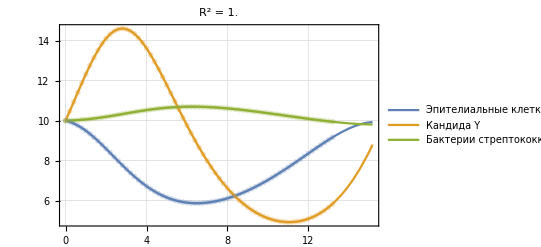

./Documents/Thesis/res/microbiota/graph_microbiota.png

```mathematica
ShowSolveLinear[preData,best,{5}]
Export["./Documents/Thesis/res/microbiota/graph_microbiota.png",%]
```

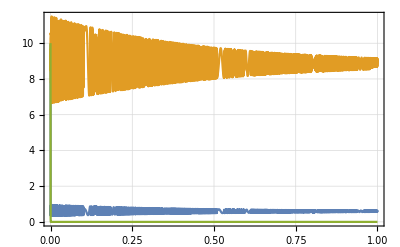

./Documents/Thesis/res/microbiota/graph_infty_zero.png

```mathematica
Plot[Evaluate[best["inf"]["Nsolution"][t]],{t,0,100+10^7},Frame->True,GridLines->Automatic,PlotRange->All]
Export["./Documents/Thesis/res/microbiota/graph_infty_zero.png",%]
```

```mathematica
A=best["A"]
```

{{0.198322,-0.0555735,-0.0297174},{-2.1188×10^-6,0.0937995,3.02686×10^-7},{-0.0223998,9.67124×10^-8,0.00319997},{-0.0000103988,-0.0652022,1.48554×10^-6}}

```mathematica
t0=0
```

0

```mathematica
pow=9
ndSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[t0],x2[t0],x3[t0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,10.^pow,10.^pow+100.}];
Nsolution=With[{$=Through[First[ndSolve[[All,All,2,0]]][#]]},$&];
```

9

```mathematica
Nsolution[10^9]
```

{0.592418,8.85399,2.8×10^-322}

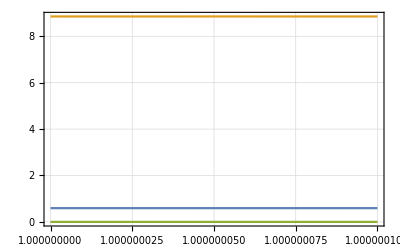

./Documents/Thesis/res/microbiota/graph_infty.png

```mathematica
Plot[Evaluate[Nsolution[t]],{t,10^9,100+10^9},Frame->True,GridLines->Automatic,PlotRange->All]
Export["./Documents/Thesis/res/microbiota/graph_infty.png",%]
```

## Picard

### iteration

```mathematica
Grid[{Join[{"Приближение"},Range[0,7]],
Join[{"R^2"},SolvePicard[#]["R"]&/@Range[0,7]]},Frame->All]
(*Export["./Documents/Thesis/res/microbiota/picard-iter.png",%,ImageSize->2000,ImageResolution->1000]*)
```

Приближение | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
R^2 | -2.24711 | -0.366191 | 0.795221 | 0.996596 | 0.999776 | 0.999978 | 0.999997 | -0.183667

```mathematica
(i↦With[{fn=Estimation[{preData,{},SolvePicard[i]["A"]},1]["Nsolution"]},Mean@CoefficientR2[fn,Transpose[preData["X"]],preData["t"]]])/@Range[7]
```

```mathematica
preData["X"]//First;
Mean@CoefficientR2[%&,Transpose[preData["X"]],preData["t"]]
```

-2.24711

### table

```mathematica
GetTable[SolvePicard[5]["confidence"]]
Export["./Documents/Thesis/res/microbiota/picard-5-iter-params.png",%,ImageSize->2000,ImageResolution->1000]
```

| Эпителиальные клетки X |  | Кандида Y |  | Бактерии стрептококков Z | 
Естественный рост | a_(RowBox[{) | -0.04406 (±0.023) | a_(RowBox[{) | -0.13797 (±0.049) | a_(RowBox[{) | 0.00609 (±0.0036)
Эпителиальные клетки X | a_(RowBox[{) | 0.00405 (±0.00037) | a_(RowBox[{) | 0.09465 (±0.00077) | a_(RowBox[{) | -0.00060 (±0.000059)
Кандида Y | a_(RowBox[{) | -0.02266 (±0.000032) | a_(RowBox[{) | -0.00009 (±0.000053) | a_(RowBox[{) | 0.00324 (±4.9×10^-6)
Бактерии стрептококков Z | a_(RowBox[{) | 0.02070 (±0.002) | a_(RowBox[{) | -0.05781 (±0.0042) | a_(RowBox[{) | -0.00306 (±0.00031)

./Documents/Thesis/res/microbiota/picard-5-iter-params.png

### graph

#### solution

```mathematica
solution=Estimation[{preData,{},SolvePicard[5]["A"]},2]["Nsolution"]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

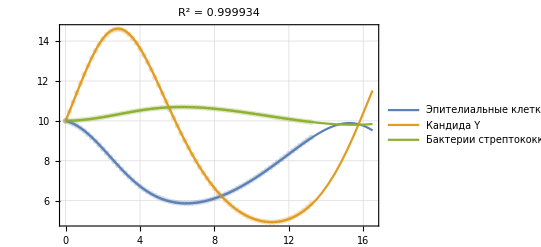

./Documents/Thesis/res/microbiota/picard-5-graph.png

```mathematica
Show[
Plot[Evaluate[solution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,20}},Frame->True,GridLines->Automatic,PlotLabel->StringForm["R^2 = ``",Mean@CoefficientR2[solution,Transpose[preData["X"]],preData["t"]]],
PlotLegends->{"Эпителиальные клетки X", "Кандида Y","Бактерии стрептококков Z"},PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"][[;;;;5]]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True]
]
Export["./Documents/Thesis/res/microbiota/picard-5-graph.png",%,ImageSize->2000,ImageResolution->1000]
```

#### solution infty 5

```mathematica
sol=Estimation[{preData,{},SolvePicard[5]["A"]},7];
solutionInfty=sol["Nsolution"];
maxT=sol["maxT"]
```

1996.81

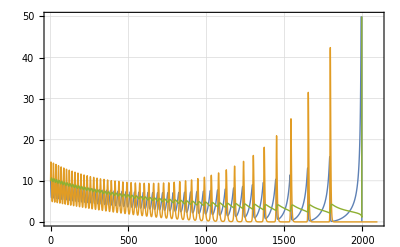

./Documents/Thesis/res/microbiota/picard-5-graph-infty-zero.png

```mathematica
Plot[Evaluate[solutionInfty[t]],{t,preData["t"]//Min,maxT+100},PlotRange->{{0,maxT+100},{0,50}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]]
Export["./Documents/Thesis/res/microbiota/picard-5-graph-infty-zero.png",%]
```

```mathematica
solutionInfty[maxT+.000001]
```

{-2.93168×10^21,0.,8.74923×10^7}

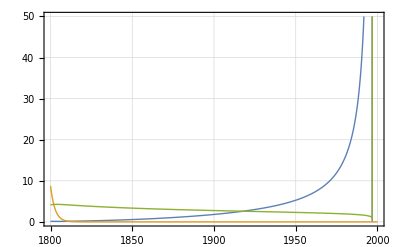

./Documents/Thesis/res/microbiota/picard-5-graph-infty-close.png

```mathematica
Plot[Evaluate[solutionInfty[t]],{t,1800,2000},PlotRange->{All,{0,50}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]]
Export["./Documents/Thesis/res/microbiota/picard-5-graph-infty-close.png",%]
```

#### solution infty 4

```mathematica
sol=Estimation[{preData,{},SolvePicard[6]["A"]},7];
solutionInfty=sol["Nsolution"];
maxT=sol["maxT"]
```

49837.4

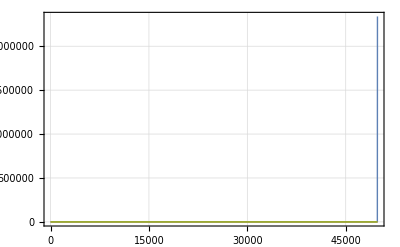

```mathematica
Plot[Evaluate[solutionInfty[t]],{t,preData["t"]//Min,maxT},PlotRange->{{0,maxT},{0,All}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]]
```

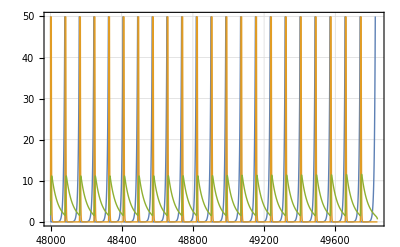

```mathematica
Plot[Evaluate[solutionInfty[t]],{t,48000,49837},PlotRange->{All,{0,50}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]]
```

# L-V experimental data PATHOG.csv

## Task

```mathematica
names={"Эпителиальные клетки X", "Комменсал Y","Патоген Z"}
```

{Эпителиальные клетки X,Комменсал Y,Патоген Z}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/danila/Documents/Thesis

```mathematica
dataRaw=Import["./data/L-V experimental data PATHOG.csv"];
```

```mathematica
dataRaw
```

### preData

```mathematica
Rest[dataRaw];
preData=<|"title"->"L-V experimental data PATHOG","names"->Rest@First[dataRaw],"X"->%[[All,2;;]],"t"->%[[All,1]],"N"->Length[%]|>
```

<|title→L-V experimental data PATHOG,names→{Epithel,Commensual,Pathog},X→{{21.7708,98.3717,29.7805},{20.4758,10.5609,31.067},{67.4628,36.261,20.5365},{22.5021,30.789,36.6855},{58.4723,6.42626,55.4899},{66.884,58.2325,28.5071},{24.2639,26.1348,46.9728}},t→{0,6,12,18,24,36,48},N→7|>

## Linear

## Solutions

```mathematica
LinearSubstitution[1]
```

{{-1.,1.},{0.5,0.5},Linear}

```mathematica
SolveLinear[preData,LinearSubstitution[1]];
MatrixConfidenceInterval[%["data"]["X"],%["data"]["Y"],%["A"]]
```

{{0.46169 (±2.3),-0.00510 (±0.028),-0.00870 (±0.028),0.00200 (±0.042)},{-0.11404 (±1.3),0.01657 (±0.017),-0.00232 (±0.017),-0.01646 (±0.025)},{0.03155 (±1.4),-0.00211 (±0.017),-0.00040 (±0.017),0.00250 (±0.025)}}

## tables

### linear

#### implicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,LinearSubstitution[i],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | -2.95 | (1.44×10^10 | 0 | 1.53×10^13)
2 | 0.148 | (0 | 0 | 6.13×10^13)
3 | -1.59×10^114 | (0 | 0 | 2.05×10^14)

#### explicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,LinearSubstitution[i,True],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 0.367 | (50.7 | 32.3 | 40.6)
2 | -1.82×10^101 | (0 | 0 | 1.32×10^14)
3 | -1.76×10^113 | (0 | 0 | 1.78×10^14)

### Adams

#### implicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,AdamsSubstitution[i],5]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | -2.95 | (1.44×10^10 | 0 | 1.53×10^13)
2 | 0.1 | (58.7 | 31.2 | 48.6)
3 | -0.0405 | (53.8 | 39.2 | 40.2)

#### explicit

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,AdamsSubstitution[i,True],5]]]/@Range[3]
],
Frame->All],3
]
```

Порядок | R^2 | Конечное состояние
1 | 0.367 | (50.7 | 32.3 | 40.6)
2 | -0.144 | (65.5 | 23.7 | 61.7)
3 | -4.4×10^107 | (2.9×10^-6 | 0 | 5.04×10^13)

### derivative

#### Central

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,DerivativeSubstitution["Central",i],6]]]/@Range[2,6,2]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
2 | -4.13×10^99 | (0 | 0 | 1.33×10^14)
4 | -58.2 | (1.9×10^14 | 1.01×10^14 | 7.82×10^13)
6 | -0.621 | (16.4 | 20.4 | 64.)

#### Forward

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],{#["inf"]["stats"][[1]]}//MatrixForm}&[SolveLinear[preData,DerivativeSubstitution["Forward",i],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | 0.367 | (50.7 | 32.3 | 40.6)
2 | 0.275 | (40.9 | 33.5 | 33.5)
3 | -11.2 | (17.7 | 201. | 0)

#### Backward

```mathematica
NumberForm[
Grid[Join[
{{"Порядок","R^2" ,"Конечное состояние"}},
Function[i,{i,#["R"],If[#["inf"]["stats"]==="не удалось","не удалось",{#["inf"]["stats"][[1]]}//MatrixForm]}&[SolveLinear[preData,DerivativeSubstitution["Backward",i],6]]]/@Range[3]
],
Frame->All],3]
```

Порядок | R^2 | Конечное состояние
1 | -8.19×10^109 | (2.01×10^-7 | 2.46×10^14 | 34.4)
2 | -1.69×10^107 | (0 | 2.47×10^14 | 1.73×10^-6)
3 | -1.04×10^114 | (100000. | 1.94×10^14 | 0.00065)

```mathematica
x=SolveLinear[preData,DerivativeSubstitution["Backward",1],6];
```

```mathematica
x["A"]//MatrixForm
{{1,2.8124772959658896*^12,0,0.029145649656206137}}.x["A"]
```

(0.0279158 | -0.3763 | -0.0508553
0.00651404 | 0.00236183 | -0.00137109
-0.00589858 | 0.00927249 | 0.0000301512
-0.00354297 | -0.0011665 | 0.00340446)

{{1.83206×10^10,6.64259×10^9,-3.85615×10^9}}

## Best

```mathematica
best=SolveLinear[preData,LinearSubstitution[1,True],7];
```

```mathematica
GetTable[best["confidence"]]
Export["./Documents/Thesis/res/pathogen/table_pathogen.png",%,ImageSize->2000,ImageResolution->500]
```

| Эпителиальные клетки X |  | Комменсал Y |  | Патоген Z | 
Естественный рост | a_(RowBox[{) | 0.25727 (±0.61) | a_(RowBox[{) | 0.08343 (±1.8) | a_(RowBox[{) | 0.05762 (±0.71)
Эпителиальные клетки X | a_(RowBox[{) | -0.00531 (±0.0055) | a_(RowBox[{) | 0.00219 (±0.016) | a_(RowBox[{) | 0.00093 (±0.0064)
Комменсал Y | a_(RowBox[{) | -0.00180 (±0.0043) | a_(RowBox[{) | -0.00545 (±0.012) | a_(RowBox[{) | 0.00032 (±0.005)
Патоген Z | a_(RowBox[{) | 0.00173 (±0.012) | a_(RowBox[{) | -0.00044 (±0.035) | a_(RowBox[{) | -0.00284 (±0.014)

./Documents/Thesis/res/pathogen/table_pathogen.png

{{50.6888,32.3269,40.6267},0,0}

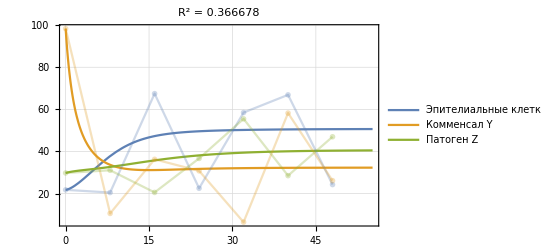

./Documents/Thesis/res/pathogen/graph_pathogen.png

```mathematica
ShowSolveLinear[preData,best,{}]
Export["./Documents/Thesis/res/pathogen/graph_pathogen.png",%]
```

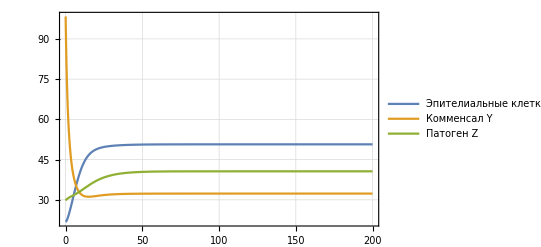

./Documents/Thesis/res/pathogen/graph_infty_zero.png

```mathematica
Plot[Evaluate[best["inf"]["Nsolution"][t]],{t,0,100+10^2},PlotLegends->names,Frame->True,GridLines->Automatic,PlotRange->All]
Export["./Documents/Thesis/res/pathogen/graph_infty_zero.png",%]
```

```mathematica
A=best["A"];
t0=0;
pow=9
ndSolve=NDSolve[{D[{x1[t],x2[t],x3[t]},t]=={x1[t],x2[t],x3[t]}*({1,x1[t],x2[t],x3[t]}.A),{x1[t0],x2[t0],x3[t0]}==First[preData["X"]]},{x1[t],x2[t],x3[t]},{t,10.^pow,10.^pow+100.}];
Nsolution=With[{$=Through[First[ndSolve[[All,All,2,0]]][#]]},$&];
```

9

```mathematica
Nsolution[10^9]
```

{0.592418,8.85399,2.8×10^-322}

```mathematica
Plot[Evaluate[Nsolution[t]],{t,10^9,100+10^9},Frame->True,GridLines->Automatic,PlotRange->All]
Export["./Documents/Thesis/res/pathogen/graph_infty.png",%]
```

-Graphics-

./Documents/Thesis/res/microbiota/graph_infty.png

## Picard

### iteration

```mathematica
Grid[{Join[{"Приближение"},Range[0,6]],
Join[{"R^2"},SolvePicard[#]["R"]&/@Range[0,7]]},Frame->All]
Export["./Documents/Thesis/res/pathogen/picard-iter.png",%,ImageSize->2000,ImageResolution->1000]
```

Приближение | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 
R^2 | -1.76229 | -9.36954 | -3.79559 | 0.694104 | 0.737334 | 0.689601 | -2.62773×10^17 | -2.32734×10^43

./Documents/Thesis/res/pathogen/picard-iter.png

```mathematica
(i↦With[{fn=Estimation[{preData,{},SolvePicard[i]["A"]},1]["Nsolution"]},Mean@CoefficientR2[fn,Transpose[preData["X"]],preData["t"]]])/@Range[7]
```

{-2.19593×10^101,-1.01401,-1.39514×10^108,-4.15112×10^105,0.223108,-1.04159,-1.60203}

```mathematica
NumberForm[{-2.1959314709491865*^101,-1.0140087722406694,-1.3951428590888825*^108,-4.1511167644764984*^105,0.22310756396681655,-1.0415890533693335,-1.6020263936837729},3]
```

{-2.2×10^101,-1.01,-1.4×10^108,-4.15×10^105,0.223,-1.04,-1.6}

### table

```mathematica
GetTable[SolvePicard[5]["confidence"]]
Export["./Documents/Thesis/res/pathogen/picard-5-iter-params.png",%,ImageSize->2000,ImageResolution->1000]
```

| Эпителиальные клетки X |  | Комменсал Y |  | Патоген Z | 
Естественный рост | a_(RowBox[{) | 0.12917 (±0.36) | a_(RowBox[{) | -0.38073 (±1.2) | a_(RowBox[{) | 0.18179 (±0.32)
Эпителиальные клетки X | a_(RowBox[{) | -0.00680 (±0.015) | a_(RowBox[{) | 0.01467 (±0.013) | a_(RowBox[{) | 0.00156 (±0.0037)
Комменсал Y | a_(RowBox[{) | -0.00005 (±0.0076) | a_(RowBox[{) | -0.00325 (±0.013) | a_(RowBox[{) | -0.00102 (±0.0054)
Патоген Z | a_(RowBox[{) | 0.00570 (±0.017) | a_(RowBox[{) | -0.00612 (±0.032) | a_(RowBox[{) | -0.00511 (±0.0083)

./Documents/Thesis/res/pathogen/picard-5-iter-params.png

### graph

```mathematica
(i↦With[{fn=Estimation[{preData,{},SolvePicard[i]["A"]},1]["Nsolution"]},Mean@CoefficientR2[fn,Transpose[preData["X"]],preData["t"]]])/@Range[6]
```

{-2.19593×10^101,-1.01401,-1.39514×10^108,-4.15112×10^105,0.223108,-1.04159}

#### solution

```mathematica
solution=Estimation[{preData,{},SolvePicard[5]["A"]},1]["Nsolution"]
```

{InterpolatingFunction[…][#1],InterpolatingFunction[…][#1],InterpolatingFunction[…][#1]}&

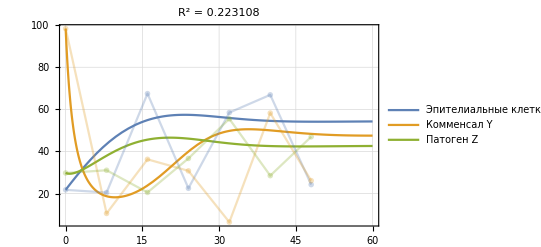

./Documents/Thesis/res/pathogen/picard-5-graph.png

```mathematica
Show[
Plot[Evaluate[solution[t]],{t,preData["t"]//Min,1.25preData["t"]//Max},PlotRange->{{0,All},{0,100}},Frame->True,GridLines->Automatic,PlotLabel->StringForm["R^2 = ``",Mean@CoefficientR2[solution,Transpose[preData["X"]],preData["t"]]],
PlotLegends->names,PlotStyle->Directive[Thick]],
ListPlot[Transpose[preData["X"]],PlotMarkers->{"OpenMarkers"},PlotStyle->Opacity[.3],
DataRange->{0,Last[preData["t"]]},Joined->True]
]
Export["./Documents/Thesis/res/pathogen/picard-5-graph.png",%,ImageSize->2000,ImageResolution->1000]
```

#### solution infty 5

```mathematica
sol=Estimation[{preData,{},SolvePicard[5]["A"]},3];
solutionInfty=sol["Nsolution"];
maxT=3000
```

3000

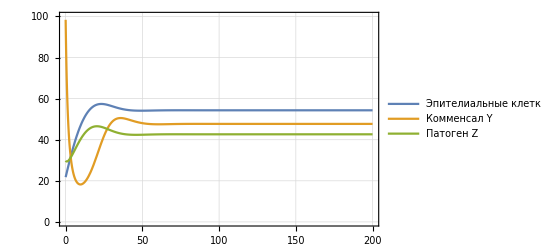

./Documents/Thesis/res/pathogen/picard-5-graph-infty-zero.png

```mathematica
Plot[Evaluate[solutionInfty[t]],{t,preData["t"]//Min,200},PlotLegends->names,PlotRange->{{0,200},{0,100}},Frame->True,GridLines->Automatic,PlotStyle->Directive[Thick]]
Export["./Documents/Thesis/res/pathogen/picard-5-graph-infty-zero.png",%]
```

```mathematica
solutionInfty[maxT]
```

{54.3194,47.6998,42.6352}